```mathematica
M = {{1,0,0,0,0,0,-1,0,0},
       {0,1,0,0,0,0,-1,0,0},
       {0,0,1,0,0,0,0,-1,0},
       {0,0,0,1,0,0,0,-1,0},
       {0,0,0,0,1,0,0,0,-1},
       {0,0,0,0,0,1,0,0,-1},
       {1,1,0,0,0,0,0,0,0},
       {0,0,1,1,0,0,0,0,0},
      {0,0,0,0,1,1,0,0,0}}
```

{{1,0,0,0,0,0,-1,0,0},{0,1,0,0,0,0,-1,0,0},{0,0,1,0,0,0,0,-1,0},{0,0,0,1,0,0,0,-1,0},{0,0,0,0,1,0,0,0,-1},{0,0,0,0,0,1,0,0,-1},{1,1,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0},{0,0,0,0,1,1,0,0,0}}

```mathematica
M//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0)

```mathematica
Det[M]
```

8

```mathematica
A={
{1,0,0,0,0,0,-1,0,0,0},
{0,1,0,0,0,0,-1,0,0,0},
{0,0,1,0,0,0,0,-1,0,0},
{0,0,0,1,0,0,0,-1,0,0},
{0,0,0,0,1,0,0,0,-1,0},
{1,0,0,0,0,0,0,0,-1,0},
{1,0,1,0,0,0,0,0,0,0},
{0,1,0,1,0,0,0,0,0,0},
{0,0,0,0,1,1,0,0,0,0},
{0,0,1,0,0,0,0,0,0,-1}
}
```

{{1,0,0,0,0,0,-1,0,0,0},{0,1,0,0,0,0,-1,0,0,0},{0,0,1,0,0,0,0,-1,0,0},{0,0,0,1,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0,-1,0},{1,0,0,0,0,0,0,0,-1,0},{1,0,1,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0},{0,0,1,0,0,0,0,0,0,-1}}

```mathematica
A //MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
Det[A]
```

```mathematica
0
```

```mathematica
A={{0,1,-1,0},{0,1,0,-1},{1,0,-1,0},{1,0,0,-1}}
```

{{0,1,-1,0},{0,1,0,-1},{1,0,-1,0},{1,0,0,-1}}

```mathematica
A//MatrixForm
```

(0 | 1 | -1 | 0
0 | 1 | 0 | -1
1 | 0 | -1 | 0
1 | 0 | 0 | -1)

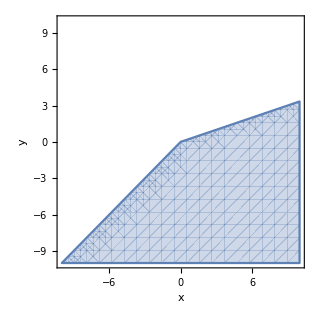

```mathematica
RegionPlot[
{3y-x<=0 &&y-x<=0},
{x,-10,10},
{y,-10,10},
Axes->True,
AxesLabel->{"x","y"}
]
```

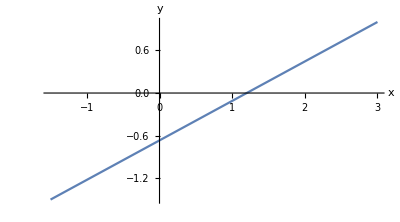

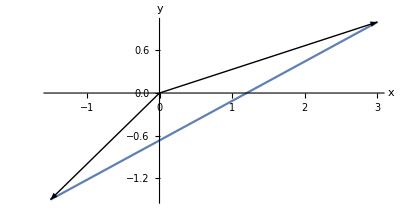

```mathematica
v={3,1};(*Replace v1,v2 with the actual components of vector v*)w={-1.5,-1.5};(*Replace w1,w2 with the actual components of vector w*)plane = ParametricPlot[a*v+(1-a)* w,{a,0,1},AxesLabel->{"x","y"},PlotRange->All,AspectRatio->Automatic]
vectors=Graphics[{Arrow[{{0,0},v}],Arrow[{{0,0},w}]}];
Show[plane,vectors]
```

```mathematica
.14g
```